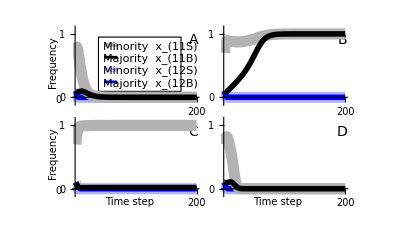

~/Fig6markers.pdf

```mathematica
(*Makes figure 8: a model where each individual has both a norm (0 or 1) and a marker (0 or 1) *)


Clear[wik,wnik, Rk, Rik, Vk, Vik, boundsimMarkers,a,m,d,g,mu,r];


boundsimMarkers[
mat1init_,(*(matrix) initial norm-marker phenotype freqs in grp 1: {{x00,x01},{x10,x11}}*)
mat2init_,(*(matrix) initial norm-marker phenotype freqs in grp 2: {{x00,x01},{x10,x11}}*)
tmax_,(*# sims*)
a_,(*prob of assorting on marker*)
m_,(*(vector) proportion of each group that is visitors*)
d_,(*(matrix) relative group sizes: how many times bigger the row group is than the column group*)
g_,(*(vector) inter-ethnic coordination payoff bonus for each group*)
mu_, (*effect of a payoff difference on copying*)
r_(*prop of population that copies norm and marker indpendently: recombination*)
]:=Module[{},

(*intialize vectors and matrices*)
mat1=mat1init;(*matrix of norm-marker phenotypes in each group*)
mat2=mat2init;
mat1all=mat1init;(*matrix holding all phenotype freqs for group 1 over time*)
mat2all=mat2init;
fit1={{1,1},{1,1}};(*fitness of phenotypes in group 1: {{x00,x01},{x10,x11}}*)
fit2={{1,1},{1,1}};
fit1all={fit1};(*matrix holding all phenotype fitnesses for group 1 over time*)
fit2all={fit2};
matg1={mat1[[1,1]],mat1[[2,2]]};(*matrix of x00 and x11 phenotypes in each group*)
matg2={mat2[[1,1]],mat2[[2,2]]};
matg1all={matg1};(*matrix holding all x00 and x11 freqs for group 1 over time*)
matg2all={matg2};



(*generalized fitness*)
Rk=(1-mk)+dnk*mnk;
Rjk=qjk*(1-mk)+qjnk*dnk*mnk;
Vk=mk+dnk*(1-mnk);
Vjk=qjk*mk+qjnk*dnk*(1-mnk);

wijk=a*((1-mk)*1/Rjk*(xnkij*dnk*mnk*(1+gk)+xkij*(1-mk)*1)+mk*1/Vjk*(xnkij*dnk*(1-mnk)*(1+gk)+xkij*mk*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+pik*mk*1));



(*simulation*)
For[t=1,t<=tmax,t++,

(*vectors of frequencies for the two groups*)
p1={mat1[[2,1]]+mat1[[2,2]],mat2[[2,1]]+mat2[[2,2]]};
p0={1-mat1[[2,1]]-mat1[[2,2]],1-mat2[[2,1]]-mat2[[2,2]]};q1={mat1[[1,2]]+mat1[[2,2]],mat2[[1,2]]+mat2[[2,2]]};
q0={1-mat1[[1,2]]-mat1[[2,2]],1-mat2[[1,2]]-mat2[[2,2]]};
x11={mat1[[2,2]],mat2[[2,2]]};
x10={mat1[[2,1]],mat2[[2,1]]};
x01={mat1[[1,2]],mat2[[1,2]]};
x00={1-mat1[[2,2]]-mat1[[2,1]]-mat1[[1,2]],1-mat2[[2,2]]-mat2[[2,1]]-mat2[[1,2]]};





For[k=1,k≤2,k++,(*loop over groups*)

If[k==1,nk=2,nk=1]; (*adjust index of other group*)


(*phenotype fitnesses*)
w11ktemp=wijk/.{
dnk->d[[nk, k]],
gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p1[[k]],pink->p1[[nk]],
qjk->q1[[k]],qjnk->q1[[nk]],
xkij->x11[[k]],xnkij->x11[[nk]]
};

w10ktemp=wijk/.{
dnk->d[[nk, k]],
gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p1[[k]],pink->p1[[nk]],
qjk->q0[[k]],qjnk->q0[[nk]],
xkij->x10[[k]],xnkij->x10[[nk]]
};
  
w01ktemp=wijk/.{
dnk->d[[nk, k]],
gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p0[[k]],pink->p0[[nk]],
qjk->q1[[k]],qjnk->q1[[nk]],
xkij->x01[[k]],xnkij->x01[[nk]]
};
  
w00ktemp=wijk/.{
dnk->d[[nk, k]],
gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p0[[k]],pink->p0[[nk]],
qjk->q0[[k]],qjnk->q0[[nk]],
xkij->x00[[k]],xnkij->x00[[nk]]
};



(*new phenotype frequencies after copying*)
x11kprime=x11k*x11k*1+
2*x11k*x10k*(0.5+mu*(w11k-w10k))+
2*x11k*x01k*(0.5+mu*(w11k-w01k))+
2*x11k*x00k*(0.5+mu*(w11k-w00k))/.{x11k->x11[[k]],x10k->x10[[k]],x01k->x01[[k]],x00k->x00[[k]],
w11k->w11ktemp,w10k->w10ktemp,w01k->w01ktemp,w00k->w00ktemp};

x10kprime=2*x10k*x11k*(0.5+mu*(w10k-w11k))+
x10k*x10k*1+
2*x10k*x01k*(0.5+mu*(w10k-w01k))+
2*x10k*x00k*(0.5+mu*(w10k-w00k))/.{x11k->x11[[k]],x10k->x10[[k]],x01k->x01[[k]],x00k->x00[[k]],
w11k->w11ktemp,w10k->w10ktemp,w01k->w01ktemp,w00k->w00ktemp};

x01kprime=2*x01k*x11k*(0.5+mu*(w01k-w11k))+
2*x01k*x10k*(0.5+mu*(w01k-w10k))+
x01k*x01k*1+
2*x01k*x00k*(0.5+mu*(w01k-w00k))/.{x11k->x11[[k]],x10k->x10[[k]],x01k->x01[[k]],x00k->x00[[k]],
w11k->w11ktemp,w10k->w10ktemp,w01k->w01ktemp,w00k->w00ktemp};

x00kprime=1-x11kprime-x10kprime-x01kprime;


(*recombination*)

(*behav and marker freqs*)
probBehav1=
x11k*x11k*1+
2*x11k*x10k*1+
2*x11k*x01k*(0.5+mu*(w11k-w01k))+
2*x11k*x00k*(0.5+mu*(w11k-w00k))+
x10k*x10k*1+
2*x10k*x01k*(0.5+mu*(w10k-w01k))+
2*x10k*x00k*(0.5+mu*(w10k-w00k))/.{x11k->x11[[k]],x10k->x10[[k]],x01k->x01[[k]],x00k->x00[[k]],
w11k->w11ktemp,w10k->w10ktemp,w01k->w01ktemp,w00k->w00ktemp};

probBehav0=1-probBehav1;

probMark1=
x11k*x11k*1+
2*x11k*x10k*(0.5+mu*(w11k-w10k))+
2*x11k*x01k*1+
2*x11k*x00k*(0.5+mu*(w11k-w00k))+
2*x10k*x01k*(0.5+mu*(w01k-w10k))+
x01k*x01k*1+
2*x01k*x00k*(0.5+mu*(w01k-w00k))/.{x11k->x11[[k]],x10k->x10[[k]],x01k->x01[[k]],x00k->x00[[k]],
w11k->w11ktemp,w10k->w10ktemp,w01k->w01ktemp,w00k->w00ktemp};

probMark0=1-probMark1;

x11krecomb=probBehav1*probMark1;
x10krecomb=probBehav1*probMark0;
x01krecomb=probBehav0*probMark1;
x00krecomb=1-x11krecomb-x10krecomb-x01krecomb;

(*combine normal and recombined subgroups*)
x11kprimeR = (1-r)*x11kprime+r*x11krecomb;
x10kprimeR = (1-r)*x10kprime+r*x10krecomb;
x01kprimeR = (1-r)*x01kprime+r*x01krecomb;
x00kprimeR=1-x11kprimeR-x10kprimeR-x01kprimeR;



(*update phenotype and fitness matrices*)
If [k==1,
{
mat1 = {{x00kprimeR,x01kprimeR},{x10kprimeR,x11kprimeR}},
fit1={{w00ktemp,w01ktemp},{w10ktemp,w11ktemp}},
matg1={x00kprimeR,x11kprimeR}
},
{
mat2 = {{x00kprimeR,x01kprimeR},{x10kprimeR,x11kprimeR}},
fit2={{w00ktemp,w01ktemp},{w10ktemp,w11ktemp}},
matg2={x00kprimeR,x11kprimeR}
}
](*if/else*)


];(*for k*)


(*accumulate phenotype freqs and fitnesses across sims*)
mat1all=Join[mat1all,mat1];
mat2all=Join[mat2all,mat2];
fit1all=Join[fit1all, fit1];
fit2all=Join[fit2all, fit2];
matg1all=Join[matg1all,{matg1}];
matg2all=Join[matg2all,{matg2}];

](*for t*)

(*Print["mat1all ",mat1all//MatrixForm];*)
(*Print["matg1all",matg1all];*)

];(*boundsimMarkers*)


(*A*************************majority controls resources*******************************)
boundsimMarkers[
mat1init={{0.7,0.1},{0.1,0.1}}, (*initial phenotype freqs in grp 1: {{x00,x01},{x10,x11}}*)
mat2init={{0.1,0.1},{0.1,0.7}},

tmax =200, (*# sims*)

a=0.9, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
r=0 (*prop pop that recombines norm and marker*)
];


(*Plots*)
x00g1=Take[mat1all[[All,1]],{1,2*tmax,2}];
x01g1=Take[mat1all[[All,1]],{2,2*tmax,2}];
x10g1=Take[mat1all[[All,2]],{1,2*tmax,2}];
x11g1=Take[mat1all[[All,2]],{2,2*tmax,2}];
x00g2=Take[mat2all[[All,1]],{1,2*tmax,2}];
x01g2=Take[mat2all[[All,1]],{2,2*tmax,2}];
x10g2=Take[mat2all[[All,2]],{1,2*tmax,2}];
x11g2=Take[mat2all[[All,2]],{2,2*tmax,2}];


Labeled[ListLinePlot[{x00g1,x01g1,x10g1,x11g1},
PlotLabel->"Group 1",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{x00g2,x01g2,x10g2,x11g2},
PlotLabel->"Group 2",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3a=
ListLinePlot[
{x01g1,x01g2,x00g1,x00g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{Blue,Opacity[0.3], Thickness[0.02]},{Blue, Thickness[0.01]},{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]} },
TicksStyle->{White,Black},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0"},{1,"1"}}}
];



(*B****************minority controlls resources*************************)
boundsimMarkers[
mat1init={{0.7,0.1},{0.1,0.1}}, (*initial phenotype freqs in grp 1: {{x00,x01},{x10,x11}}*)
mat2init={{0.1,0.1},{0.1,0.7}},

tmax =200, (*# sims*)

a=0.9, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.1,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
r=0 (*prop pop that recombines norm and marker*)
];


(*Plots*)
x00g1=Take[mat1all[[All,1]],{1,2*tmax,2}];
x01g1=Take[mat1all[[All,1]],{2,2*tmax,2}];
x10g1=Take[mat1all[[All,2]],{1,2*tmax,2}];
x11g1=Take[mat1all[[All,2]],{2,2*tmax,2}];
x00g2=Take[mat2all[[All,1]],{1,2*tmax,2}];
x01g2=Take[mat2all[[All,1]],{2,2*tmax,2}];
x10g2=Take[mat2all[[All,2]],{1,2*tmax,2}];
x11g2=Take[mat2all[[All,2]],{2,2*tmax,2}];


Labeled[ListLinePlot[{x00g1,x01g1,x10g1,x11g1},
PlotLabel->"Group 1",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{x00g2,x01g2,x10g2,x11g2},
PlotLabel->"Group 2",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3b=
ListLinePlot[
{x01g1,x01g2,x00g1,x00g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{Blue,Opacity[0.3], Thickness[0.02]},{Blue, Thickness[0.01]},{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]} },
TicksStyle->{White,White},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0",{0,0}},{1,"1",{0,0}}}}
];



(*C************************minority homeland*****************************)
boundsimMarkers[
mat1init={{0.7,0.1},{0.1,0.1}}, (*initial phenotype freqs in grp 1: {{x00,x01},{x10,x11}}*)
mat2init={{0.1,0.1},{0.1,0.7}},

tmax =200, (*# sims*)

a=0.7, (*prob of assorting on marker*)
m={0.1,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
r=0 (*prop pop that recombines norm and marker*)
];


(*Plots*)
x00g1=Take[mat1all[[All,1]],{1,2*tmax,2}];
x01g1=Take[mat1all[[All,1]],{2,2*tmax,2}];
x10g1=Take[mat1all[[All,2]],{1,2*tmax,2}];
x11g1=Take[mat1all[[All,2]],{2,2*tmax,2}];
x00g2=Take[mat2all[[All,1]],{1,2*tmax,2}];
x01g2=Take[mat2all[[All,1]],{2,2*tmax,2}];
x10g2=Take[mat2all[[All,2]],{1,2*tmax,2}];
x11g2=Take[mat2all[[All,2]],{2,2*tmax,2}];


Labeled[ListLinePlot[{x00g1,x01g1,x10g1,x11g1},
PlotLabel->"Group 1",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{x00g2,x01g2,x10g2,x11g2},
PlotLabel->"Group 2",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3c=
ListLinePlot[
{x01g1,x01g2,x00g1,x00g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{Blue,Opacity[0.3], Thickness[0.02]},{Blue, Thickness[0.01]},{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]} },
TicksStyle->{Black,Black},
Ticks->{{{100,""},{200,"200"}},{{0,"0"},{1,"1"}}}
];


(*D************************minority homeland, lots of visitors*****************************)
boundsimMarkers[
mat1init={{0.7,0.1},{0.1,0.1}}, (*initial phenotype freqs in grp 1: {{x00,x01},{x10,x11}}*)
mat2init={{0.1,0.1},{0.1,0.7}},

tmax =200, (*# sims*)

a=0.7, (*prob of assorting on marker*)
m={0.4,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5,(*effect of a payoff difference on copying*)
r=0 (*prop pop that recombines norm and marker*)
];


(*Plots*)
x00g1=Take[mat1all[[All,1]],{1,2*tmax,2}];
x01g1=Take[mat1all[[All,1]],{2,2*tmax,2}];
x10g1=Take[mat1all[[All,2]],{1,2*tmax,2}];
x11g1=Take[mat1all[[All,2]],{2,2*tmax,2}];
x00g2=Take[mat2all[[All,1]],{1,2*tmax,2}];
x01g2=Take[mat2all[[All,1]],{2,2*tmax,2}];
x10g2=Take[mat2all[[All,2]],{1,2*tmax,2}];
x11g2=Take[mat2all[[All,2]],{2,2*tmax,2}];


Labeled[ListLinePlot[{x00g1,x01g1,x10g1,x11g1},
PlotLabel->"Group 1",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{x00g2,x01g2,x10g2,x11g2},
PlotLabel->"Group 2",
PlotLegends->{"x00", "x01","x10","x11"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3d=
ListLinePlot[
{x01g1,x01g2,x00g1,x00g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{Blue,Opacity[0.3], Thickness[0.02]},{Blue, Thickness[0.01]},{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]} },
TicksStyle->{Black,White},
Ticks->{{{100,""},{200,"200"}},{{0,"0",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(****************************************assemble plots into Fig 8*)
Fig6markers=Panel[
GraphicsGrid[
{{f3a,f3b},{f3c,f3d}},

Spacings->{
{
Scaled[0.4],
Scaled[0],
Scaled[0.2]
},
{
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["A",14],{380,-45}],
Inset[Style["B",14],{740,-45}],
Inset[Style["C",14],{380,-270}],
Inset[Style["D",14],{740,-270}],
Inset[Rotate[Style["Frequency",10],90Degree],{40,-100}],
Inset[Rotate[Style["Frequency",10],90Degree],{40,-320}],
Inset[Style["Time step",10],{225,-440}],
Inset[Style["Time step",10],{585,-440}],
Inset[Style["0",10],{54,-190}],
Inset[Style["0",10],{54,-412}],

x1=-35;
y1=40;
{EdgeForm[Thin],White,Rectangle[{185+x1,-78+y1},{385+x1,-210+y1}]},
Inset[Style["Minority ",10]Subscript[Style["x",Italic,10],Style["11S",Italic,8]],{310+x1,-100+y1}],
Inset[Style["Majority ",10]Subscript[Style["x",Italic,10],Style["11B",Italic,8]],{310+x1,-130+y1}],
Inset[Style["Minority ",10]Subscript[Style["x",Italic,10],Style["12S",Italic,8]],{310+x1,-160+y1}],
Inset[Style["Majority ",10]Subscript[Style["x",Italic,10],Style["12B",Italic,8]],{310+x1,-190+y1}],
{AbsoluteThickness[3],GrayLevel[0.7],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[2],Black,Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.3],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[2],Blue,Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["~/Fig6markers.pdf",Fig6markers,"PDF"]
(*Export["/Users/johnbunce/Desktop/Fig6.pdf",Fig6,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
*)
```